```mathematica
Table[1/2 KroneckerDelta[i,j],{i,1,20},{j,0,19}]+Table[1/2 KroneckerDelta[i,j],{i,0,19},{j,1,20}]
```

```mathematica
T={{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1/2}};
```

```mathematica
T//MatrixForm
```

(1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2)

```mathematica
p0=Table[KroneckerDelta[i,10],{i,1,20}]
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

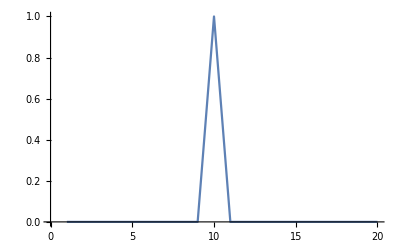

```mathematica
ListLinePlot[p0]
```

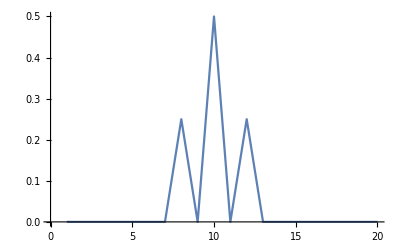

```mathematica
ListLinePlot[T.T. p0]
```

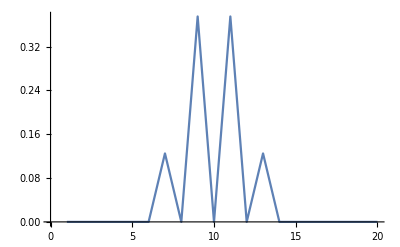

```mathematica
ListLinePlot[T.T.T. p0]
```

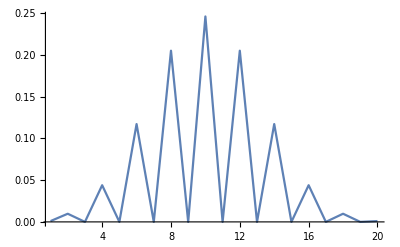

```mathematica
ListLinePlot[MatrixPower[T,10]. p0,PlotRange->Full]
```

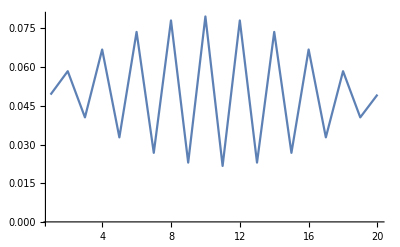

```mathematica
ListLinePlot[MatrixPower[T,100]. p0,PlotRange->Full]
```

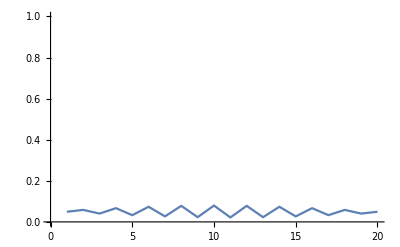

```mathematica
ListLinePlot[MatrixPower[T,100]. p0,PlotRange->{0,1}]
```